```mathematica
number:=Table[If[x<10,"0"<>ToString[x],ToString[x]],{x,0,99}];classical =Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\classical\\classical.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
jazz =Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\jazz\\jazz.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
rock=Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\rock\\rock.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
hiphop=Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\hiphop\\hiphop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
pop = Table[File["C:\\Users\\oscar\\Documents\\ML\\EmelineOscarProjectMusic\\genres.tar\\genres\\genres\\pop\\pop.000"<>ToString[number⟦x⟧]<>".au"],{x,100}];
popTest = Drop[pop,92];
pop = Drop[pop,-8];
classicalTest = Drop[classical,92];
classical = Drop[classical,-8];
rockTest = Drop[rock,92];
rock = Drop[rock,-8];
jazzTest = Drop[jazz,92];
jazz = Drop[jazz,-8];
hiphopTest = Drop[hiphop,92];
hiphop = Drop[hiphop,-8];
```

```mathematica
genres = {"classical","jazz","rock","hiphop","pop"};
musicGenres = Flatten[Table[Table[genres⟦x⟧,92],{x,5}]];
testGenres = Flatten[Table[Table[genres⟦x⟧,8],{x,5}]];
musicTest = Join[classicalTest,jazzTest,rockTest,hiphopTest,popTest];
```

```mathematica
data = RandomSample[Thread[Join[classical,jazz,rock,hiphop,pop]-> musicGenres]];
validation = Thread[musicTest-> testGenres];
```

```mathematica
(*données pour tests*)
```

```mathematica
Clear[rnnNet]
rnnNet = NetInitialize@NetChain[{
LongShortTermMemoryLayer[400],
SequenceLastLayer[],
LinearLayer[100],
Ramp,
LinearLayer[5],
SoftmaxLayer[]
},"Input"->NetEncoder[{"AudioSpectrogram"}],
"Output"-> NetDecoder[{"Class", genres}]]
```

NetChain[<>]

```mathematica
trained = NetTrain[rnnNet,data,BatchSize -> 3,MaxTrainingRounds->10, TargetDevice->"GPU"]
```

NetChain[<>]

ClassifierMeasurementsObject[…]

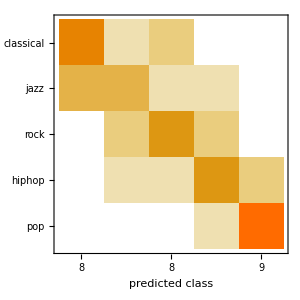

0.575

```mathematica
measurements = ClassifierMeasurements[trained,validation]
measurements["ConfusionMatrixPlot"]
measurements["Accuracy"]
```

```mathematica
Clear[audio]
audio = AudioCapture[]
```

```mathematica
trained[audio, "Probabilities"]
```

<|classical→0.10265,jazz→0.0487729,rock→0.00279741,hiphop→0.658916,pop→0.186863|>

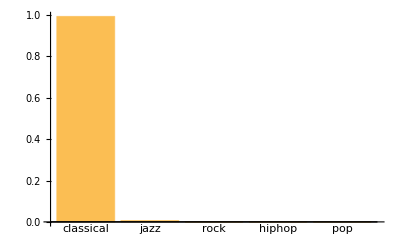

```mathematica
a = Import["C:\\Users\\oscar\\OneDrive\\Documents\\Wolfram\\genres\\classical\\classical.00098.au"]

BarChart[trained[a,"Probabilities"],ChartLabels-> genres]
```

```mathematica
NetChain[<>]
```

```mathematica
Export["rnnNet.wlnet",trained]
```

rnnNet.wlnet